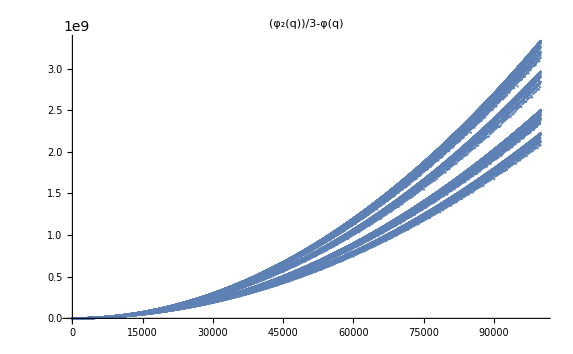
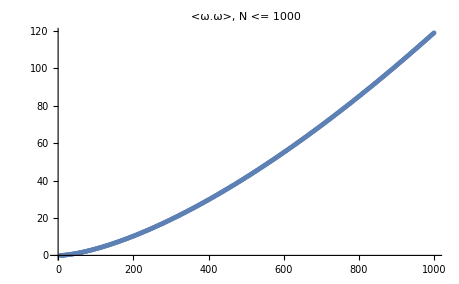
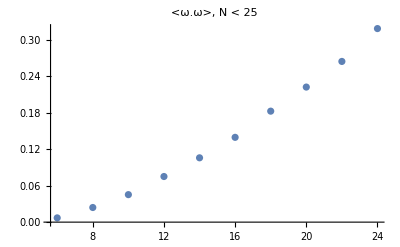
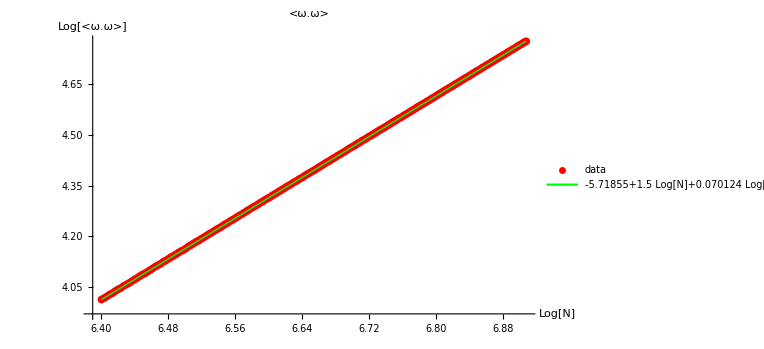
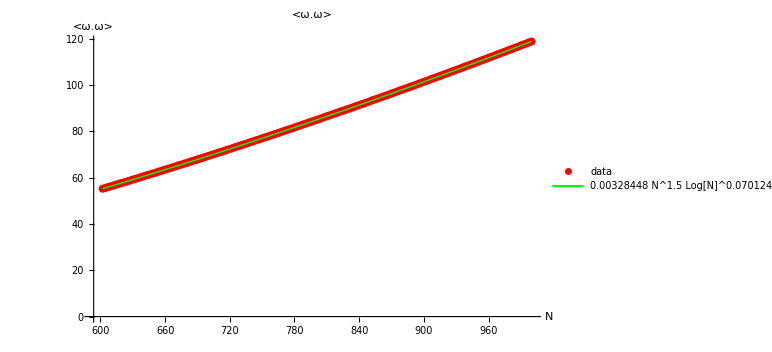
```mathematica
(*This is the first chapter of my notebooks for my decaying turbulence  paper 
"TO THE THEORY OF DECAYING TURBULENCE" submitted to the MDPI Fractals and Fractions special issue*)
Sqr[F_] := Expand[F.F]
F[k_] := {u[k],v[k], I b} (* anzatz*)
Eq3 =FullSimplify[Sqr[F[k+1] - F[k]]-1]
-1+(u[k]-u[1+k])^2+(v[k]-v[1+k])^2

(* My way around bugs in  ReIm[] *)
MyReIm[Ex_] := ReIm[ComplexExpand[Ex]]/.{Im[X_]:>0, Re[X_] :>X}
Eq4 =(Sqr[F[k+1]] - Sqr[F[k]] - I γ)^2 + γ^2-Sqr[F[k+1] + F[k]]
4 b^2+γ^2-u[k]^2-2 u[k] u[1+k]-u[1+k]^2-v[k]^2-2 v[k] v[1+k]-v[1+k]^2+(-ⅈ γ-u[k]^2+u[1+k]^2-v[k]^2+v[1+k]^2)^2
{Eq4R , Eq4I} =MyReIm[Eq4]//FullSimplify
{4 b^2+u[k]^4-2 u[k] u[1+k]+u[1+k]^4+(-1+(v[k]-v[1+k])^2) (v[k]+v[1+k])^2+u[1+k]^2 (-1-2 v[k]^2+2 v[1+k]^2)-u[k]^2 (1+2 u[1+k]^2-2 v[k]^2+2 v[1+k]^2),2 γ (u[k]^2-u[1+k]^2+v[k]^2-v[1+k]^2)}
(* we see that Eq4I is satisfied if u^2 + v^2 does not depend on k *)
Sub = {u[l_] :> r Cos[α[l]], v[l_] :> r Sin[α[l]]}
{u[l_]:>r Cos[α[l]],v[l_]:>r Sin[α[l]]}
Eq4I/.Sub//FullSimplify
0
(* now we have to look for solutions for α[k], r, b *)
Eq5 =Eq4R/.Sub//FullSimplify
4 b^2-2 r^2-2 r^2 Cos[α[k]-α[1+k]]
Eq6 =Eq3 /.Sub//FullSimplify
-1+2 r^2-2 r^2 Cos[α[k]-α[1+k]]
ClearAll[β];
rbsol =Simplify[Solve[{Eq5==0, Eq6==0}, {b, r}][[-1]]/.α[k]-α[1+k]->-β,{0 < β < Pi}]//TrigReduce
{b->1/2 Cot[β/2],r->1/(√2 √(1-Cos[β]))}
(* here is our symmetric solution *)
ff[k_, α_, β_] =FullSimplify[(F[k]/.Sub/.rbsol),0 < β < Pi]
{1/2 Cos[α[k]] Csc[β/2],1/2 Csc[β/2] Sin[α[k]],1/2 ⅈ Cot[β/2]}
df[k_, α_, β_] := ff[k+1, α, β]- ff[k, α, β];
Redsimp[X_] := FullSimplify[X/.{α[n_+1] :> α[n] + β σ }]/.{Cos[x_ σ]:>Cos[x],Sin[x_ σ]:>σ  Sin[x],σ^2->1};
Redsimp[ff[k, α, β].df[k, α, β]]
-1/2

Redsimp[df[k, α, β].df[k, α, β]]
1
Redsimp[(ff[k, α, β].ff[k, α, β])]
1/4
ClearAll[TT];
TT:= {TensorProduct[FF,DF] , TensorProduct[DF,FF], TensorProduct[DF,DF], II};
Sub= {A_⊗DF:>A  u -v/2 A,A_⊗FF:>A (-u/2) + A v/4,II->DF u + FF v}

{A_⊗DF:>A u-(v A)/2,A_⊗FF:>1/2 A (-u)+(A v)/4,II->DF u+FF v}
RR = Distribute[(#/.Sub)& /@ TT]
{8 FF u-4 FF v,-4 DF u+2 DF v,8 DF u-4 DF v,8 DF u+8 FF v}
""
""
Ca = {I,(2 γ+ 3 I),(2 I -γ),2 λ + γ};
Cb = {-I,(2 γ+  I),γ,-2 λ - γ};
LHS =Collect[Expand[Ca.RR ],{u,v}]
u (4 ⅈ DF+8 ⅈ FF-8 DF γ+16 DF λ)+v (-2 ⅈ DF-4 ⅈ FF+8 DF γ+8 FF γ+16 FF λ)
RHS =Collect[Expand[Cb.RR ],{u,v}]
u (-4 ⅈ DF-8 ⅈ FF-8 DF γ-16 DF λ)+v (2 ⅈ DF+4 ⅈ FF-8 FF γ-16 FF λ)
Collect[#,{u,v}]& /@ExpandAll /@{(LHS/2==RHS/2)/.{DF->1,FF->0} , (LHS/4==RHS/4)/.{DF->0,FF->1} }
{v (-ⅈ+4 γ)+u (2 ⅈ-4 γ+8 λ)==ⅈ v+u (-2 ⅈ-4 γ-8 λ),
2 ⅈ u+v (-ⅈ+2 γ+4 λ)==-2 ⅈ u+v (ⅈ-2 γ-4 λ)}
EQ3 ={(RHS==LHS ⅇ^((2 ⅈ l π)/N))/.{DF->1,FF->0}  ,(RHS==LHS ⅇ^((2 ⅈ l π)/N))/.{DF->0,FF->1} }
{2 ⅈ v+u (-4 ⅈ-8 γ-16 λ)==ⅇ^((2 ⅈ l π)/N) (v (-2 ⅈ+8 γ)+u (4 ⅈ-8 γ+16 λ)),-8 ⅈ u+v (4 ⅈ-8 γ-16 λ)==ⅇ^((2 ⅈ l π)/N) (8 ⅈ u+v (-4 ⅈ+8 γ+16 λ))}
sol =FullSimplify[Solve[EQ3/.u->1,{v,λ}],{l,N} ϵ Integers]
{{v->2,λ->-γ/2},{v->-(2 ⅈ (1+ⅇ^((2 ⅈ l π)/N)))/(-ⅈ+ⅇ^((2 ⅈ l π)/N) (-ⅈ+4 γ)),λ->1/2 ⅈ γ Tan[(l π)/N]}}
λ/.sol
{-γ/2,1/2 ⅈ γ Tan[(l π)/N]}
psi =FullSimplify [#,{{l, N} ϵ Integers, γ ϵ Reals}]&/@( {1,v}/.sol)
{{1,2},{1,-(2 ⅈ (1+ⅇ^((2 ⅈ l π)/N)))/(-ⅈ+ⅇ^((2 ⅈ l π)/N) (-ⅈ+4 γ))}}
MyReIm[Ex_] := ReIm[ComplexExpand[Ex]]/.{Im[X_]:>0, Re[X_] :>X}
MyNorm[{u_,v_}] :=MyReIm[Abs[u]^2 + Abs[v]^2/4 - Re[u v]][[1]];
FullSimplify [#,{{l, N} ϵ Integers, γ ϵ Reals}]&/@(MyNorm /@ psi)
psi
MyReIm[1 + I x]
{1,x}
MyNorm[{-ⅈ+ⅇ^((2 ⅈ l π)/N) (-ⅈ+4 γ),-2 ⅈ (1+ⅇ^((2 ⅈ l π)/N))}]
4+8 Cos[(2 l π)/N]+4 Cos[(2 l π)/N]^2+16 γ^2 Cos[(2 l π)/N]^2-16 γ Sin[(2 l π)/N]-16 γ Cos[(2 l π)/N] Sin[(2 l π)/N]+16 γ^2 Sin[(2 l π)/N]^2
FullSimplify [MyNorm[{-ⅈ+ⅇ^((2 ⅈ l π)/N) (-ⅈ+4 γ),-2 ⅈ (1+ⅇ^((2 ⅈ l π)/N))}],{{l, N} ϵ Integers, γ ϵ Reals}]
2 (3+8 γ^2+4 Cos[(2 l π)/N]+Cos[(4 l π)/N]-32 γ Cos[(l π)/N]^3 Sin[(l π)/N])
Sum[t^(I γ/2 Tan[Pi l/N]),{l,1,N-1}]
∑_(l=1)^(-1+N) t^(1/2 ⅈ γ Tan[(l π)/N])
GG[τ_, k_] := 1/Pi 2 Pi I Assuming[{k ϵ Integers, k >0},Residue[(Exp[I τ u](1 + I u)^(k-1))/(1- I u)^(1+k),{u,-I}]]
GG[τ,k]
2 ⅈ Residue[ⅇ^(ⅈ u τ) (1-ⅈ u)^(-1-k) (1+ⅈ u)^(-1+k),{u,-ⅈ}]
D[x^(k-1),{x,n}]
x^(-1+k-n) FactorialPower[-1+k,n]
FullSimplify /@ Table[1/k!D[E^(x z)(1+x)^(k-1),{x,k}]/.x->1,{k,5}]
{ⅇ^z z,ⅇ^z z (1+z),1/3 ⅇ^z z (3+2 z (3+z)),1/3 ⅇ^z z (3+z (3+z)^2),1/15 ⅇ^z z (15+2 z (30+z (30+z (10+z))))}
FullSimplify[(2E^z /k!Sum[Binomial[k,n]z^(k-n) FactorialPower[-1+k,n],{n,0,k}])/.z->-γ Log[t+t0]/2]
(2 (-1)^k (t+t0)^(-γ/2) HypergeometricU[-k,0,1/2 γ Log[t+t0]])/(k!)
(* compute vorticity vector *)
Cross[ff[k,α,β],ff[k+1,α,β]]
{1/4 ⅈ Cot[β/2] Csc[β/2] Sin[α[k]]-1/4 ⅈ Cot[β/2] Csc[β/2] Sin[α[1+k]],-1/4 ⅈ Cos[α[k]] Cot[β/2] Csc[β/2]+1/4 ⅈ Cos[α[1+k]] Cot[β/2] Csc[β/2],-1/4 Cos[α[1+k]] Csc[β/2]^2 Sin[α[k]]+1/4 Cos[α[k]] Csc[β/2]^2 Sin[α[1+k]]}
(* make it simpler *)
FullSimplify[I Cross[ff[k,α,β],ff[k+1,α,β]]/.{α[k+1]-> α[k] + σ β}]/.{Sin[σ β]-> σ Sin[β], Sin[σ β/2]-> σ Sin[β/2]}//Simplify
{1/2 σ Cos[(β σ)/2+α[k]] Cot[β/2],1/2 σ Cot[β/2] Sin[(β σ)/2+α[k]],1/2 ⅈ σ Cot[β/2]}
(* this is a lightlike vectotr (zero square))*)
FullSimplify[Sqr[Cross[ff[k,α,β],ff[k+1,α,β]]]]//.{α[k+1]-> α[k] + σ[k] β, Cos[β σ[k]]->Cos[β]}
0
(* the general formula for dissipation on the solution of recurrent equations*)
Diss =Expand[Subscript[F, k].Subscript[F, k] - 1/4(σ Sqrt[4 Subscript[F, k].Subscript[F, k] + γ(2 I - γ)] - I γ)^2]/.σ^2->1//FullSimplify
1/2 γ (γ+ⅈ (-1+σ √(-γ (-2 ⅈ+γ)+4 Subscript[F, k].Subscript[F, k])))
1/2 γ (γ+ⅈ (-1+σ √(-γ (-2 ⅈ+γ)+4 Subscript[F, k].Subscript[F, k])))
1/2 γ (γ+ⅈ (-1+σ √(-γ (-2 ⅈ+γ)+4 Subscript[F, k].Subscript[F, k])))
(* check how it vanishes on a symmetric soluion *)
Test =FullSimplify[Diss//.{Subscript[F, k].Subscript[F, k] ->1/4}]
1/2 γ (γ+ⅈ (-1+√(-(-ⅈ+γ)^2) σ))
FullSimplify[Test/.√(-(-ⅈ+γ)^2)->I (γ -I)]
-1/2 γ (-ⅈ+γ) (-1+σ)
FullSimplify[ff[k+1,M] - ff[k,M]]
-ff[k,M]+ff[1+k,M]
(ff[k+1,M] - ff[k,M]).(ff[k+1,M] - ff[k,M])//FullSimplify
(-ff[k,M]+ff[1+k,M]).(-ff[k,M]+ff[1+k,M])
(* linearized discrete loop equations*)
(*vector version of ReIm *)

(* This is the second chapter *)




RHS[P_, ΔP_, γ_] := -γ^2 (ΔP.ΔP) P + γ^2 (P.ΔP) ΔP + I γ ΔP ((ΔP.P)^2/(ΔP.ΔP)- P.P);
SetDelayed::write: "Tag \!\(\*RowBox[{\"Plus\"}]\) in \!\(\*RowBox[{RowBox[{\"(\", RowBox[{RowBox[{\"-\", FractionBox[\"T2\", RowBox[{\"2\", \" \", SuperscriptBox[\"λ\", \"2\"]}]]}], \"-\", FractionBox[\"T1\", \"λ\"]}], \")\"}], \"[\", RowBox[{\"P_\", \",\", \"ΔP_\", \",\", \"γ_\"}], \"]\"}]\) is Protected."
Leq =CoefficientList[Normal[Series[RHS[P + ϵ Q, ΔP + ϵ ΔQ, γ] ,{ϵ,0,1}]],ϵ]
{(-T2/(2 λ^2)-T1/λ)[P,ΔP,γ],ΔQ (Derivative[0,1,0][(-T2/(2 λ^2)-T1/λ)])[P,ΔP,γ]+Q (Derivative[1,0,0][(-T2/(2 λ^2)-T1/λ)])[P,ΔP,γ]}
{γ^2 ΔP P.ΔP+ⅈ γ ΔP (-P.P+(ΔP.P)^2/(ΔP.ΔP))-P γ^2 ΔP.ΔP,
γ^2 (Q ΔP 1.ΔP+ΔP ΔQ P.1+ΔQ P.ΔP)+ⅈ γ (ΔP (-Q 1.P-Q P.1+((-ΔQ 1.ΔP-ΔQ ΔP.1) (ΔP.P)^2)/(ΔP.ΔP)^2+(2 (ΔQ 1.P+Q ΔP.1) ΔP.P)/(ΔP.ΔP))+ΔQ (-P.P+(ΔP.P)^2/(ΔP.ΔP)))-γ^2 (P ΔQ 1.ΔP+P ΔQ ΔP.1+Q ΔP.ΔP)}
{γ^2 ΔP P.ΔP+ⅈ γ ΔP (-P.P+(ΔP.P)^2/(ΔP.ΔP))-P γ^2 ΔP.ΔP,γ^2 (Q ΔP 1.ΔP+ΔP ΔQ P.1+ΔQ P.ΔP)+ⅈ γ (ΔP (-Q 1.P-Q P.1+((-ΔQ 1.ΔP-ΔQ ΔP.1) (ΔP.P)^2)/(ΔP.ΔP)^2+(2 (ΔQ 1.P+Q ΔP.1) ΔP.P)/(ΔP.ΔP))+ΔQ (-P.P+(ΔP.P)^2/(ΔP.ΔP)))-γ^2 (P ΔQ 1.ΔP+P ΔQ ΔP.1+Q ΔP.ΔP)}
Leqt=(Leq[[2]]/(2t γ))/.{P ->F, ΔP -> ΔF}//Expand
(ΔQ (Derivative[0,1,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/(2 t γ)+(Q (Derivative[1,0,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/(2 t γ)
(* Q = G t^(-λ)*)
EigenEq0 = λ G +ExpandAll[Leqt]//.{Q ->G, ΔQ-> ΔG,ΔF.ΔF->1,F.F ->1/4(γ^2+ (2 F.ΔF- I γ)^2),
G X_1.ΔF :>X G.ΔF,G X_ ΔF .1 :>X G.ΔF,ΔG  X_1.ΔF :> X ΔG .ΔF,ΔG  X_ ΔF .1 :>X ΔG .ΔF,
G X_1.F :> X G.F,G X_ F .1 :>X G.F,ΔG  X_1.F :> X ΔG .F,ΔG  X_ F .1 :>X ΔG .F, t->1}
G λ+(ΔG (Derivative[0,1,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/(2 γ)+(G (Derivative[1,0,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/(2 γ)
EigenEq=FullSimplify[2 EigenEq0]
(2 G γ λ+ΔG (Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]+G (Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ])/γ
ReqEq=Collect[Expand[EigenEq//.{  
F.G :> (F.g1 + F.g)/2, F.ΔG :>F.g1 - F.g,
ΔF.G :> (ΔF.g1 +ΔF.g)/2, ΔF.ΔG :>ΔF.g1 - ΔF.g}]/.{G -> g1/2 + g/2, ΔG -> g1 - g}, {g1, F.g1, ΔF.g1}]
g λ-(g (Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ])/γ+(g (Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ])/(2 γ)+g1 (λ+((Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ])/γ+((Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ])/(2 γ))
ClearAll[A, B];
B[g_] =FullSimplify[( ReqEq/.{F.g1 -> 0,ΔF.g1 -> 0  })/.g1->0]
(g (2 γ λ-2 (Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]+(Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]))/(2 γ)
A[g1_] =FullSimplify[( -ReqEq+ B[g])]

-(g1 (2 γ λ+2 (Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]+(Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]))/(2 γ)
ExpandAll[A[g1]]/.{ΔF.F->F.ΔF, 1.F -> ⊗F,X_ F.1 :> F⊗X,1.ΔF -> ⊗ΔF,X_ ΔF.1 :> ΔF⊗X}
-g1 λ-(g1 (Derivative[0,1,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/γ-(g1 (Derivative[1,0,0][(-T2/(2 λ^2)-T1/λ)])[F,ΔF,γ])/(2 γ)
(* doing it myself!!!*)
(II γ)/2-II λ+1/2 ⅈ  ΔF ⊗F+γ F⊗ΔF-1/2 γ ΔF ⊗ΔF+1/2 ⅈ   F⊗ΔF- γ  F⊗ΔF-2 ⅈ  ΔF ⊗F F.ΔF+ⅈ  ΔF ⊗ΔF (F.ΔF)^2+ γ ΔF⊗F-ⅈ  F.ΔF ΔF⊗ΔF+ⅈ   (F.ΔF)^2 ΔF⊗ΔF//FullSimplify
1/2 (II (γ-2 λ)+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF)))
(II (γ-2 λ)+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF)))/.λ->0

II γ+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF))
(* 2 A =*)II γ+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF))
II γ+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF))
FullSimplify[Expand[B[g]/.{ΔF.F->F.ΔF}]/.{F.g -> ⊗F, ΔF.g -> ⊗ΔF}]
(g (2 γ λ-2 (Derivative[0,1,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]+(Derivative[1,0,0][(-(T2+2 T1 λ)/(2 λ^2))])[F,ΔF,γ]))/(2 γ)
(* 2 B = *)(-γ+2 λ-(ⅈ+2 γ)  F⊗ΔF-ⅈ  (ΔF+4 ΔF F.ΔF)⊗F+ (2 F γ+γ ΔF+2 ⅈ ΔF (F.ΔF)^2)⊗ΔF+2 ΔF⊗(F γ+ⅈ ΔF F.ΔF (1+F.ΔF)) )//FullSimplify
-γ+2 λ-(ⅈ+2 γ) F⊗ΔF+2 ΔF⊗(F γ+ⅈ ΔF F.ΔF (1+F.ΔF))-ⅈ (ΔF+4 ΔF F.ΔF)⊗F+(2 F γ+γ ΔF+2 ⅈ ΔF (F.ΔF)^2)⊗ΔF
(* 2 B = *)-γ+2 λ-(ⅈ+2 γ) F⊗ΔF+2 ΔF⊗(F γ+ⅈ ΔF F.ΔF (1+F.ΔF))-ⅈ (ΔF+4 ΔF F.ΔF)⊗F+(2 F γ+γ ΔF+2 ⅈ ΔF (F.ΔF)^2)⊗ΔF
-γ+2 λ-(ⅈ+2 γ) F⊗ΔF+2 ΔF⊗(F γ+ⅈ ΔF F.ΔF (1+F.ΔF))-ⅈ (ΔF+4 ΔF F.ΔF)⊗F+(2 F γ+γ ΔF+2 ⅈ ΔF (F.ΔF)^2)⊗ΔF
TensorRules={(A_ + B_)⊗ C_ :> A⊗ C +  B⊗ C, C_⊗ (A_ + B_) :> C⊗ A+  C⊗B, 
(F⊗ X_ F):> X F⊗F,(ΔF⊗ X_ F):> X ΔF⊗F ,
(F⊗ X_ ΔF):> X F⊗ΔF,(ΔF⊗ X_ ΔF):> X ΔF⊗ΔF ,
(X_ F⊗ ΔF):> X F⊗ΔF,(X_ ΔF⊗  ΔF):> X ΔF⊗ΔF ,
(X_ F⊗  F):> X F⊗F,(X_ ΔF⊗  F):> X ΔF⊗F ,
(2 F γ)⊗ΔF -> 2 γ  F⊗ΔF,ΔF⊗(F γ)-> γ ΔF⊗F ,
ΔF⊗(ⅈ ΔF (F.ΔF)^2)-> ⅈ  (F.ΔF)^2 ΔF⊗ΔF,
(γ ΔF)⊗ΔF -> γ ΔF⊗ΔF, (4 ΔF F.ΔF)⊗F -> 4  F.ΔF ΔF⊗F,
(2 ⅈ ΔF (F.ΔF)^2)⊗ΔF ->2 ⅈ  (F.ΔF)^2 ΔF⊗ΔF,
ΔF⊗(ⅈ ΔF F.ΔF) -> (ⅈ F.ΔF)ΔF⊗ΔF
}
{(A_+B_)⊗C_:>A⊗C+B⊗C,C_⊗(A_+B_):>C⊗A+C⊗B,F F⊗X_:>X F⊗F,F ΔF⊗X_:>X ΔF⊗F,ΔF F⊗X_:>X F⊗ΔF,ΔF ΔF⊗X_:>X ΔF⊗ΔF,F⊗ΔF X_:>X F⊗ΔF,ΔF⊗ΔF X_:>X ΔF⊗ΔF,F⊗F X_:>X F⊗F,ΔF⊗F X_:>X ΔF⊗F,(2 F γ)⊗ΔF->2 γ F⊗ΔF,ΔF⊗(F γ)->γ ΔF⊗F,ΔF⊗(ⅈ ΔF (F.ΔF)^2)->ⅈ ΔF⊗ΔF (F.ΔF)^2,(γ ΔF)⊗ΔF->γ ΔF⊗ΔF,(4 ΔF F.ΔF)⊗F->4 ΔF⊗F F.ΔF,(2 ⅈ ΔF (F.ΔF)^2)⊗ΔF->2 ⅈ ΔF⊗ΔF (F.ΔF)^2,ΔF⊗(ⅈ ΔF F.ΔF)->ⅈ ΔF⊗ΔF F.ΔF,F.ΔF->-1/2}
(* 2 B = *)FullSimplify[(ExpandAll[(-γ+2 λ-(ⅈ+2 γ)  F⊗ΔF-ⅈ  (ΔF+4 ΔF F.ΔF)⊗F+ (2 F γ+γ ΔF+2 ⅈ ΔF (F.ΔF)^2)⊗ΔF+2 ΔF⊗(F γ+ⅈ ΔF F.ΔF (1+F.ΔF)) )]//.TensorRules)/.{F.ΔF ->-1/2,λ->0}]
-ⅈ F⊗ΔF+(ⅈ+2 γ) ΔF⊗F+γ (-1+ΔF⊗ΔF)
(* 2 A =*)(γ+ⅈ F⊗ΔF+ΔF⊗F (ⅈ+2 γ-4 ⅈ F.ΔF)-ΔF⊗ΔF (γ-2 ⅈ F.ΔF (-1+2 F.ΔF)))/.F.ΔF ->-1/2
γ+ⅈ F⊗ΔF+(3 ⅈ+2 γ) ΔF⊗F-(-2 ⅈ+γ) ΔF⊗ΔF



(* Inversion of the LHS matrix*)
AA[γ_, λ_] := (2 λ + γ) II + I FDF + (2 γ + 3 I) DFF +(2 I - γ)DFDF + 0 FF;
(* Generic form of the inverse matrix  MM = 1/AA*)
MM[γ_, λ_] := X0 II +X1 FDF + X2 DFF + X3 DFDF + X4 FF;
(* Algebraic substitution in AA matrix to multiply by MM matrix*)
Alg = {
II ->    {II,FDF,DFF,DFDF,FF},
FDF ->  {FDF,-1/2FDF,FF,FDF,-1/2FF},
DFF ->  {DFF,1/4 DFDF,-1/2DFF,-1/2DFDF,1/4DFF},
DFDF ->{DFDF,-1/2DFDF,DFF,DFDF,-1/2 DFF},
FF->       {FF, 1/4 FDF, -1/2 FF, -1/2 FDF, 1/4 FF}
}

{II->{II,FDF,DFF,DFDF,FF},FDF->{FDF,-FDF/2,FF,FDF,-FF/2},DFF->{DFF,DFDF/4,-DFF/2,-DFDF/2,DFF/4},DFDF->{DFDF,-DFDF/2,DFF,DFDF,-DFF/2},FF->{FF,FDF/4,-FF/2,-FDF/2,FF/4}}
(* result for AA.MM, expanded in the basis II,FDF,DFF,DFDF,FF*)
AAMM=Grad[(AA[γ,λ]/.Alg).{X0,X1,X2,X3,X4},{II,FDF,DFF,DFDF,FF}]
{X0 (γ+2 λ),ⅈ X0+ⅈ X3+X1 (-ⅈ/2+γ+2 λ),X0 (3 ⅈ+2 γ)+X4 (1/2 (-2 ⅈ+γ)+1/4 (3 ⅈ+2 γ))+X2 (2 ⅈ+1/2 (-3 ⅈ-2 γ)+2 λ),X0 (2 ⅈ-γ)+X1 (1/2 (-2 ⅈ+γ)+1/4 (3 ⅈ+2 γ))+X3 (2 ⅈ+1/2 (-3 ⅈ-2 γ)+2 λ),ⅈ X2+X4 (-ⅈ/2+γ+2 λ)}
(* equations for coefficints Xk: AA.MM = II*)
Eqs = Thread[AAMM=={1,0,0,0,0}]
{X0 (γ+2 λ)==1,ⅈ X0+ⅈ X3+X1 (-ⅈ/2+γ+2 λ)==0,X0 (3 ⅈ+2 γ)+X4 (1/2 (-2 ⅈ+γ)+1/4 (3 ⅈ+2 γ))+X2 (2 ⅈ+1/2 (-3 ⅈ-2 γ)+2 λ)==0,X0 (2 ⅈ-γ)+X1 (1/2 (-2 ⅈ+γ)+1/4 (3 ⅈ+2 γ))+X3 (2 ⅈ+1/2 (-3 ⅈ-2 γ)+2 λ)==0,ⅈ X2+X4 (-ⅈ/2+γ+2 λ)==0}
Xsol=Solve[Eqs,{X0,X1,X2,X3,X4}][[1]]
{X0->-1/(-γ-2 λ),X1->(ⅈ (-3 ⅈ+4 λ))/(2 (γ-2 λ) (γ+2 λ)^2),X2->((3 ⅈ+2 γ) (-ⅈ+2 γ+4 λ))/(2 (γ-2 λ) (γ+2 λ)^2),X3->-(-3-6 ⅈ γ+4 γ^2-16 ⅈ λ+8 γ λ)/(4 (γ-2 λ) (γ+2 λ)^2),X4->-(ⅈ (3 ⅈ+2 γ))/((γ-2 λ) (γ+2 λ)^2)}
(* Inverse matrix MM expanded in the basis *)
Eq1=FullSimplify[(MM[γ,λ]/.Xsol)/.Alg]
{1/(4 (γ-2 λ) (γ+2 λ)^2)(6 (DFF+FDF+2 FF)+4 γ (-2 ⅈ FF+II γ+2 DFF (ⅈ+γ))+8 (ⅈ (3 DFF+FDF)+2 DFF γ) λ-16 II λ^2+DFDF (3+6 ⅈ γ-4 γ^2-8 (-2 ⅈ+γ) λ)),(DFDF (-ⅈ+4 γ)+2 FDF (-ⅈ+2 γ-4 λ))/(4 (γ^2-4 λ^2)),(ⅈ (DFF+2 FF+2 ⅈ DFF γ+4 ⅈ DFF λ))/(2 (γ^2-4 λ^2)),(ⅈ (DFDF+2 FDF+2 ⅈ DFDF γ+4 ⅈ DFDF λ))/(2 (γ^2-4 λ^2)),(DFF (-ⅈ+4 γ)+2 FF (-ⅈ+2 γ-4 λ))/(4 (γ^2-4 λ^2))}

(* Now, the RHS matrix in the same basis*)
BB[γ_, λ_] := -(2 λ + γ) II - I FDF + (2 γ +  I) DFF + γ DFDF + 0 FF;
(* Inverse matrix times B: MM.BB in our basis*)
FullSimplify[(-γ^2+4 λ^2)Grad[Eq1.{-(2λ+ γ), -I,(2 γ + I), γ, 0},{II,FDF,DFF,DFDF,FF}]]
{γ^2-4 λ^2,2,2 (ⅈ+γ) (-ⅈ+2 γ+4 λ),1+2 ⅈ γ+4 ⅈ λ,4-4 ⅈ γ}
Collect[FullSimplify[(γ^2-4 λ^2)Eq1.{-(2λ+ γ), -I,(2 γ + I), γ, 0}],{II,FDF,DFF,DFDF,FF}]
-2 FDF+FF (-4+4 ⅈ γ)-ⅈ DFDF (-ⅈ+2 γ+4 λ)-2 DFF (ⅈ+γ) (-ⅈ+2 γ+4 λ)+II (-γ^2+4 λ^2)

(* Third chapter. The Multitotients *)

S[q_] :=Simplify[Plus @@ (Cot[Pi #/q]^2 & /@ Select[Range[q-1],GCD[#,q]==1&])];
Phi2[q_] := q^2 Times @@ ((1 - 1/#[[1]]^2)&/@ FactorInteger[q]);
SBM[q_?IntegerQ] := 1/3 Phi2[q]-EulerPhi[q];
SBM[22071945]
135744984254976
FullSimplify[S[100]]//Timing
{63.237729,2360}
SBM[100]//Timing
{0.00014,2360}
SMdata={#,SBM[#]}& /@ Range[10,100000];
ListPlot[SMdata,PlotLabel->Subscript[φ,2][q]/3-φ[q]]
-Graphics-

SBM[9]
18
9^2(1-1/9)/3 -9(1-1/3)
18
Table[{q,SBM[q]},{q,2,10}]
{{2,0},{3,2/3},{4,2},{5,4},{6,6},{7,10},{8,12},{9,18},{10,20}}
6^2(1-1/9)(1-1/4)/3 = (3-1)(3+1)(2-1)(2+1)/3
8
Table[Phi2[q]/3,{q,3,20}]
{8/3,4,8,8,16,16,24,24,40,32,56,48,64,64,96,72,120,96}
SBM[2^64+1]
113427455638803936117726648213506949120
SBM[2^64]
85070591730234615856620279821087277056
SBM[2^128+1]
38597363079105398474523661669562625103150274109036501299425668761748925317120
SBM[Prime[200000]]
2521122091602
SBM[Prime[200000]+1]
1580590852608

(* Fourth chapter. Multicotangent sums *)


(*https://link.springer.com/article/10.1007/s40993-021-00250-4, Theorem 2.1*)
S[n_,N_] := Sum[Cot[Pi j/N]^(2 n),{j,N-1}];
ClearAll[BernSum];
BernSum[0,0] = 1;
BernSum[n_,m_] /; m>n:= 0;
BernSum[n_, m_] := Sum[BernoulliB[2 j1]/(2 j1)!BernoulliB[2 j2]/(2 j2)!
BernSum[n-1, m-j1-j2] ,{j1,0,m},{j2,0,m-j1}];
A[n_,N_] :=(-1)^n N - (-1)^n 2^(2 n)Sum[BernoulliB[2 j0]/(2 j0)!BernSum[n,n-j0] N^(2 j0),{j0,0,n}];
N[S[5,1000],30]
2.13770936983164138961642188000000000000006674`30.*^25
N[S[5,1000] ,30]
2.13770936983164138961642188000000000000006674`30.*^25
A[5,1000]
74071629664177500742510069418/3465
N[A[5,1000],30]
2.13770936981753248896132956473304473304473304`30.*^25
Table[BernoulliB[2 j],{j,0,10}]
{1,1/6,-1/30,1/42,-1/30,5/66,-691/2730,7/6,-3617/510,43867/798,-174611/330}
BernSum[1,0]
1
BernSum[4,1] 
2/3
Sum[BernoulliB[2 j0]/(2 j0)!BernoulliB[2 j1]/(2 j1)!With[{j2 = 1-j0-j1},BernoulliB[2 j2]/(2 j2)!],{j0,0,1},{j1,0,1-j0}]
1/4
A[1,N]//FullSimplify
1/3 (-2+N) (-1+N)
Table[A[n,m],{n,3}]//FullSimplify//TableForm
{{1/3 (-2+m) (-1+m)}, {1/45 (-23+m (45-20 m+m^3))}, {1/945 (396+m (-945+462 m-42 m^3+2 m^5))}}
S[1,N]
1/3 (-2+N) (-1+N)
DirSum[n_,m_] :=
Block[{pp},
pp =Select[Range[m-1],GCD[#,m] ==1& ];
Plus @@( Cot[Pi  pp/m]^(2 n))
];
SBM[n_,N_] :=(-1)^n Phi[1,N]- (-1)^n 2^(2 n)Sum[BernoulliB[2 j0]/(2 j0)!BernSum[n,n-j0] Phi[2 j0,N],{j0,1,n}];
Table[SBM[n,N] ,{n,8}]
{-Phi[1,N]+1/3 Phi[2,N],Phi[1,N]-4/9 Phi[2,N]+1/45 Phi[4,N],-Phi[1,N]+22/45 Phi[2,N]-2/45 Phi[4,N]+2/945 Phi[6,N],Phi[1,N]-(1436 Phi[2,N])/2835+43/675 Phi[4,N]-(16 Phi[6,N])/2835+Phi[8,N]/4725,-Phi[1,N]+(21757 Phi[2,N])/42525-(136 Phi[4,N])/1701+(424 Phi[6,N])/42525-(2 Phi[8,N])/2835+(2 Phi[10,N])/93555,Phi[1,N]-(11368 Phi[2,N])/22275+(3982 Phi[4,N])/42525-(13136 Phi[6,N])/893025+1/675 Phi[8,N]-(8 Phi[10,N])/93555+(1382 Phi[12,N])/638512875,-Phi[1,N]+(35874836 Phi[2,N])/70945875-(147668 Phi[4,N])/1403325+(37556 Phi[6,N])/1913625-(748 Phi[8,N])/297675+(292 Phi[10,N])/1403325-(2764 Phi[12,N])/273648375+(4 Phi[14,N])/18243225,Phi[1,N]-(318710248 Phi[2,N])/638512875+(661489442 Phi[4,N])/5746615875-(1552016 Phi[6,N])/63149625+(16811 Phi[8,N])/4465125-(35272 Phi[10,N])/88409475+(114706 Phi[12,N])/4104725625-(64 Phi[14,N])/54729675+(3617 Phi[16,N])/162820783125}
Table[SBM[n,N] ,{n,3}]//FullSimplify//TableForm
{{1/3 (-3 Phi[1,N]+Phi[2,N])}, {Phi[1,N]+1/45 (-20 Phi[2,N]+Phi[4,N])}, {1/945 (-945 Phi[1,N]+462 Phi[2,N]-42 Phi[4,N]+2 Phi[6,N])}}
ClearAll[Phi];
Tot[n_,q_] := q^n Times @@ ((1 - 1/#[[1]]^n)&/@ FactorInteger[q]);
SBM[7,100000]/.Phi->Tot
414789494549371629813494523106760042908028471565960064688789283640000/189189
N[DirSum[5,1000],20]
2.13562175117519294480476000000000000000006676`20.*^25
SBM[5,1000]/.Phi->Tot
4036325109694867136069546800/189
N[SBM[5,1000]/.Phi->Tot, 20]
2.13562175116130536299976021164021164021164021`20.*^

(* Fifth Chapter. Computations of enstrophy
*)


FF[A_] =FullSimplify[1/2Sum[σ E^(- I ω σ  + I E^(I β σ A)),{σ,-1,1,2}],{β,ω, A} ϵ Reals]
(-ⅈ Cos[Cos[A β]]+Sin[Cos[A β]]) Sin[ω-ⅈ Sin[A β]]

(* this substitution compotes the Fourier integral over unit circle *)
subInt[r_, l_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==I r,l][[1]])}
{ⅇ^X_ F_:>(F/.Solve[D[X, ω]==ⅈ r,l]⟦1⟧)}
(* This is a binomial expansion of the power of the cosine, to use above substitution rule*)
II =1/2FullSimplify[TrigToExp[Cos[ω]^(N-2)(1-Cos[2 ω])]/.(ⅇ^(-ⅈ ω)+ⅇ^(ⅈ ω))^(-2+N) -> Binomial[N-2,l] E^(I ω (N-2-l) - I ω l) ]//Expand
-2^-N ⅇ^(-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]+2^(1-N) ⅇ^(2 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]-2^-N ⅇ^(4 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]
JJ = II/.subInt[-q r, l]
-2^-N Binomial[-2+N,1/2 (-4+N+q r)]+2^(1-N) Binomial[-2+N,1/2 (-2+N+q r)]-2^-N Binomial[-2+N,1/2 (N+q r)]
(* this is to help silly Mathematica simplify sum of binomials*)
KK = Binomial[-2+N,1/2 (-2+N+q r)] FullSimplify[JJ/Binomial[-2+N,1/2 (-2+N+q r)]]
(2^(2-N) (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N+q r)])/(N^2-q^2 r^2)
(* this time it simplifies without human intervention*)
F2[β_,q_, r_, N_]  =N(N-1)/(2 * 16)(2^(2-N) (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N+q r)])/(N^2-q^2 r^2)//FullSimplify
(2^(-5-N) (N-q^2 r^2) Gamma[1+N])/(Gamma[1/2 (2+N-q r)] Gamma[1/2 (2+N+q r)])
FullSimplify /@ Asymptotic[F2[β,q, z Sqrt[N]/q, N],{N , Infinity,2}]
-(ⅇ^(-z^2/2) √N (-1+z^2))/(16 √(2 π))+(ⅇ^(-z^2/2) (-1+z^2) (3-6 z^2+z^4))/(192 √N √(2 π))-(ⅇ^(-z^2/2) (-1+z) (1+z) (45-660 z^2+570 z^4-108 z^6+5 z^8))/(23040 N^(3/2) √(2 π))
EE =1/2 Integrate[(√N)/(16 √(2 π)) N^3/(3 *3 Zeta[3])E^(-μ N),{N,0, Infinity}, GenerateConditions->False]
35/(1536 √2 μ^(9/2) Zeta[3])
Zlim =Asymptotic[ Binomial[N,N/2]2^(-N) N^2/( 2 Zeta[2]),N->Infinity]
(3 √2 N^(3/2))/π^(5/2)

ZZ =1/2 Integrate[Zlim  E^(- μ N),{N,0,Infinity}, GenerateConditions->False]
9/(4 √2 π^2 μ^(5/2))
(* result for r=0 contributrion to the enstrophy*)
result = EE/ZZ
(35 π^2)/(3456 μ^2 Zeta[3])
N[(35 π^2)/(3456 μ^2 Zeta[3]),10]
(0.08315129725122778758817153626646535343`10.)/μ^2
(* now the hard part-- averaging over the Euler ensemble *)
SumP[F_, q_,r_, M_]:= 
Block[{betas, ints},
betas = N[Select[Range[q-1],GCD[#,q]==1&]2 Pi/q,20];
ints =  F[#,q r, M]& /@ betas;
(Plus @@  ints)
];

EulerSum[F_, M_] := Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)SumP[F,q,r,M]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}];

PartitionFunction[M_]:=
PartitionFunction[M]=
Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)EulerPhi[q]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}]
EulerAverage[F_, M_] := EulerSum[F,M]/PartitionFunction[M];

EulerAverage[F2, 1000]
118.86270222802317864345868296750763576119`17.2148176913544
(* this takes a few minutes or half an hour, depending of number of cores*)
ParallelTable[PartitionFunction[M],{M,3,1000}];

F2data = ParallelTable[EulerAverage[F2,M],{M,4,1000}];
F2data[[;;2]] (* garbage, too low M*)
{0``41.596870903509576,-0.00325520833333333333333333333333333334`19.139350763337735}
f2test=Take[Transpose[{Range[4,1000],F2data}],{3,-1,2}];
f2test[[1]]
{6,0.0069835574127906976744186046511627907`18.983496610082305}
Dimensions[f2test]
{498,2}
ListPlot[f2test,PlotLabel->"<ω.ω>, N <= 1000"]
-Graphics-
f2test[[10]]
{24,0.31798101602223720920143451841308278934`18.790537774559628}
ListPlot[f2test[[;;10]],PlotLabel->"<ω.ω>, N < 25"]
-Graphics-
f2model = LinearModelFit[Log[f2test[[-200;;]]],{x},x]
FittedModel[-«59»+«59» x]
Normal[f2model]
-5.65567732246692912450156129375410754765`17.894061024863735+1.51052186123510035705646578378391441571`17.894061024863735 x

f2meanmodel = NonlinearModelFit[Log[f2test[[-200;;]]],{a + b Log[x]+ 1.5 x},{a, b},x]
FittedModel[«1»]
Normal[f2meanmodel]
-5.7185481735211185+1.5 x+0.07012396515116472 Log[x]
ShowLogFitModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[model[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{model[Log[N]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"Log[N]", "Log[<ω.ω>]"}
];
ShowFitLogModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{Exp[model[Log[N]]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<ω.ω>"}
];

ShowLogFitModel[Log[f2test[[-200;;]]],f2meanmodel,"<ω.ω>"]
-Graphics-
ShowFitLogModel[f2test[[-200;;]],f2meanmodel,"<ω.ω>"]
-Graphics-
f2meanmodel["ParameterTable"]
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"1059.0994343207653`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {a, -5.7185481735211185, 0.001959838742430816, -2917.8666844948284, 0.}, {b, 0.07012396515116472, 0.0010324200669177177, 67.92193158402982, 3.8651847251390446*^-139}}
Exp[f2meanmodel[Log[N]]]
0.003284475931635543 N^1.5 Log[N]^0.07012396515116472
(*


@misc{MB23,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/SphericalThetaIntegral.nb},author={Alexander Migdal},title={Restricted O(3) Fourier Integral},year={2023},month={06}}


@misc{MB24,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/ThetaIntegral.nb},author={Alexander Migdal},title={Matrix Fourier Transform in S3},year={2023},month={06}}

@misc{MB25,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/SaddlePointFourierIntegral.nb},author={Alexander Migdal},title={Saddle Point Matrix Fourier Integral in S3},year={2023},month={07}}

@misc{MB26,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/PadeBorel.nb},author={Alexander Migdal},title={Pade Borel with Cosh and Sinh integrals},year={2023},month={07}}

@misc{MB27,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/CorrFunctionIntegrals.nb},author={Alexander Migdal},title={Corr Function Integrals},year={2023},month={07}}

@misc{MB28,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/AnalyticSolutionEnstrophy.nb},author={Alexander Migdal},title={Analytic Solution for Enstrophy},year={2023},month={08}}
@misc{MB29,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/Enstrophy%20Computations.nb},author={Alexander Migdal},title={Enstrophy Computations},year={2023},month={08}}


@misc{MB30,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/EnstrophyEuler.nb},author={Alexander Migdal},title={Euler Partition Function},year={2023},month={08}}

@misc{MB31,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/TestMultitotients.nb},author={Alexander Migdal},title={Sum Cotangent Squared},year={2023},month={08}}



@misc{MB32,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/MultifractalSpectrum.nb},author={Alexander Migdal},title={Multifractal Spectrum},year={2023},month={08}}



@misc{MB33,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/Momets%20of%20vorticity.nb},author={Alexander Migdal},title={Moments of Vorticity},year={2023},month={09}}


@misc{MB34,howpublished={https://www.wolframcloud.com/obj/\\ sasha.migdal/Published/ClosedEigenLoop.nb},author={Alexander Migdal},title={ClosedEigenLoop},year={2023},month={09}}
*)
```